```mathematica
a=1.5
b=1
c=1/(a b)
m=N[(a+b+c)/3]
e=N[((a-b)^2+(b-c)^2+(c-a)^2)/3]
```

1.5

1

0.666667

1.05556

0.351852

```mathematica
NDSolve[{y''[x]+15 y'[x] y[x]+18 (y[x]^3-1)==0,y[0]==m,y'[0]==-e},y,{x,0,1}]
```

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
DSolve[{54 z[x]+15 z'[x]+z''[x]==0,z[0]==A-1,z'[0]==-B},z[x],x]
```

{{z[x]→1/3 ⅇ^(-9 x) (6-6 A+B-9 ⅇ^(3 x)+9 A ⅇ^(3 x)-B ⅇ^(3 x))}}

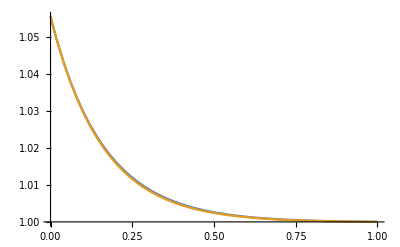

```mathematica
Plot[{Evaluate[y[x]/.%],1+1/3 Exp[-9 x] (6 (1-m)+e+(9 (m-1)-e) Exp[3 x])},{x,0,1}]
```